```mathematica
Quit[]
```

#### Get component function (temporary)

```mathematica
Needs["Olveretal`"];
ClearAll[GetComponent]
Options[GetComponent]={Coordinates->"Spherical",Mute->True};
GetComponent[solvec_List,expr_List,layer_Integer,layout_List,n_Integer,OptionsPattern[]]:=
Block[{position,subdomain,nsubdomains,partition,zeroInDomain,startindex,listParity,listExtracted,(*options*) coordinates},

(* set up options *)
coordinates=OptionValue[Coordinates];
If[!OptionValue[Mute],
If[SameQ[coordinates,"Spheroidal"],Print["Spheroidal coordinates"],Print["Spherical coordinates"]]
];

(* recover subdomains from model *)
partition=Partition[Sort(*@Rest*)[Sprouts`domain],2,1];
nsubdomains=Length[partition];
Table[subdomain[i]=partition⟦i⟧,{i,1,Length[partition]}];
If[SameQ[N@First[subdomain[1]],0.],zeroInDomain=True,zeroInDomain=False];

(* find component position in solution vector *)
position=Flatten@Position[layout,Alternatives@@expr];

(* find parity of fields accross the origin based on their indices of spherical harmonics *)
listParity=
Block[{out},
If[zeroInDomain&&SameQ[layer,1],
Which[
SameQ[coordinates,"Spheroidal"],
Which[
MatchQ[#,f_[ℓ_,𝓂_]/;EvenQ[ℓ+𝓂]],out="even";,
MatchQ[#,f_[ℓ_,𝓂_]/;OddQ[ℓ+𝓂]],out="odd";,
True,Print["error with parity !"]
],
SameQ[coordinates,"Spherical"],
Which[
MatchQ[#,f_[ℓ_,𝓂_]/;EvenQ[ℓ]],out="even";,
MatchQ[#,f_[ℓ_,𝓂_]/;OddQ[ℓ]],out="odd";,
True,Print["error with parity !"];
],
True,Print["error with coordinates !"];
]
];
out
]&/@expr;

(* extracted elements from solution vector *)
listExtracted=
Block[{extracted},
If[zeroInDomain,
startindex=Max[(layer-3/2)*n*Length[layout]+1,1];
If[SameQ[layer,1],
extracted=Take[solvec⟦startindex;;startindex+Length[layout]n/2-1⟧,{(#-1)*n/2+1,#*n/2}],
extracted=Take[solvec⟦startindex;;startindex+Length[layout]n-1⟧,{(#-1)*n+1,#*n}]
],
startindex=(layer-1)*n*Length[layout]+1;
extracted=Take[solvec⟦startindex;;startindex+Length[layout]n-1⟧,{(#-1)*n+1,#*n}]
]
]&/@position;

(* output: riffle with zeroes if zero is in first layer *)
If[zeroInDomain&&SameQ[layer,1],
Table[
Switch[listParity⟦i⟧,
"even",N@Riffle[listExtracted⟦i⟧,0.+0.ⅈ],
"odd",N@Riffle[listExtracted⟦i⟧,0.+0.ⅈ,{1,-1,2}],
True,Print["error with Riffle !"]
]
,{i,1,Length[expr]}],
N@listExtracted
]

]
```

Get::noopen: Cannot open Olveretal`.

Needs::nocont: Context Olveretal` was not created when Needs was evaluated.

# Free-decay modes

## Load fennec & spectral package

```mathematica
SetDirectory[NotebookDirectory[]];
Needs["spectral`","../spectral.m"];
Needs["sprouts`","../sprouts.m"];
```

## Call to fennec

```mathematica
η[r_]:=ⅇ^(-r^2)(*r^4*)(*Cos[2π r]*);ricb=0.35;
(*With[{𝓂=0,ℓ=2},
ℒ={((ℓ (1+ℓ) η[r])/r^2-λ) F[ℓ,𝓂][r]-(2 η[r] F[ℓ,𝓂]'[r])/r-η[r] F[ℓ,𝓂]''[r]};
ℬ={F[ℓ,𝓂]'[1]+(ℓ+1)F[ℓ,𝓂][1]==0,ricb F[ℓ,𝓂]'[ricb]-ℓ F[ℓ,𝓂][ricb]==0};
𝒱={F[ℓ,𝓂]}
];*)
With[{𝓂=0,ℓ=2},
ℒ={(G[ℓ,𝓂][r] (-ℓ (1+ℓ) η[r]+r (r λ+η'[r])))/r^2+((2 η[r])/r+η'[r]) G[ℓ,𝓂]'[r]+η[r] G[ℓ,𝓂]''[r]};
ℬ={G[ℓ,𝓂][1]==0,G[ℓ,𝓂][ricb]==0};
𝒱={G[ℓ,𝓂]}
];
```

```mathematica
A=SproutsFun[Join[ℒ,ℬ],𝒱,{r,ricb,1},160,eigenvalue->λ]
```

partition of the spatial domain :  {{0.35,1}}

eigenvalue problem of type :   (A0+A1 λ)x==0

Size of output matrices :  160x160

{SparseArray[…],SparseArray[…]}

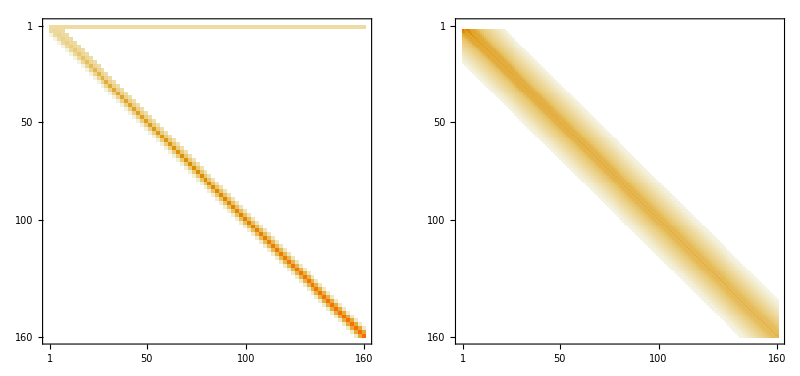

```mathematica
GraphicsRow[MatrixPlot/@Abs[A]]
```

## Solve and post-process

```mathematica
target=(*1.306078;*)(*0.611984935;*)(*0.6018079098587724-0.004710037467145376 ⅈ;*)1;
```

```mathematica
{eig,eigv}=SortBy[Eigensystem[{A⟦1⟧,-A⟦2⟧}]ᵀ,First]ᵀ//Chop;
eigv=Delete[eigv,Position[eig,ComplexInfinity]];
eig=Delete[eig,Position[eig,ComplexInfinity]];
```

```mathematica
eig
```

{22.0467,66.357,137.265,235.929,362.609,517.376,700.252,911.249,1150.37,1417.62,1712.99,2036.5,2388.13,2767.89,3175.78,3611.81,4075.96,4568.24,5088.65,5637.2,6213.87,6818.67,7451.6,8112.67,8801.86,9519.19,10264.6,11038.2,11839.9,12669.8,13527.8,14413.9,15328.1,16270.5,17241.,18239.6,19266.3,20321.2,21404.3,22515.4,23654.7,24822.1,26017.6,27241.3,28493.1,29773.,31081.1,32417.3,33781.6,35174.1,36594.6,38043.3,39520.2,41025.2,42558.3,44119.5,45708.9,47326.4,48972.,50645.7,52347.6,54077.6,55835.8,57622.1,59436.5,61279.,63149.7,65048.5,66975.4,68930.5,70913.6,72925.,74964.4,77032.,79127.7,81251.5,83403.5,85583.6,87791.8,90028.2,92292.7,94585.3,96906.1,99255.,101632.,104037.,106470.,108932.,111421.,113939.,116485.,119059.,121659.,124290.,126957.,129638.,132374.,135094.,138006.,140866.,143967.,147365.,150145.,154931.,157758.,163129.,166548.,171598.,178255.,181475.,190205.,193254.,202112.,210037.,215515.,228116.,230925.,245047.,255182.,264196.,281724.,285643.,307793.,321112.,335351.,362056.,367919.,401672.,423009.,446291.,488234.,496806.,555438.,590729.,626792.,705867.,719468.,820034.,897031.,963781.,1.11941×10^6,1.14027×10^6,1.36641×10^6,1.54601×10^6,1.65926×10^6,2.08925×10^6,2.13126×10^6,2.6731×10^6,3.3441×10^6,3.67283×10^6,5.03937×10^6,5.39223×10^6,7.99001×10^6,1.22897×10^7,1.29585×10^7,2.95369×10^7,3.28568×10^7,7.89459×10^7,∞,∞}

```mathematica
pos=1;
```

```mathematica
(* extract components from solution *)
ClearAll[out,outnull]
Block[{list,coef,assoc=<||>,pos=pos},
Table[
list[layer]=Sprouts`layout⟦layer⟧;
coef[layer]=Chop@GetComponent[eigv⟦pos⟧,list[layer],layer,Sprouts`layout⟦layer⟧,Sprouts`nr];
AppendTo[assoc,AssociationThread[list[layer],coef[layer]]]
,{layer,1,Sprouts`nlayers}];
out=assoc;
]
outnull=Map[(#)->ConstantArray[0,Sprouts`nr]&,Keys[out]/.f_[ℓ_,𝓂_]->f[ℓ-1,𝓂]]~Join~Map[(#)->ConstantArray[0,Sprouts`nr]&,Keys[out]/.f_[ℓ_,𝓂_]->f[ℓ+1,𝓂]];
AppendTo[out,outnull];
```

```mathematica
ClearAll[NChebevalC]
NChebevalC[c_][x_]:=NChebeval[N[Re[c]]][x]+ⅈ NChebeval[N[Im[c]]][x]
xk=Cos[((2Range[1,Sprouts`nr]-1)π)/(2Sprouts`nr)]//N;
rk=Sprouts`rfu[1][xk];
```

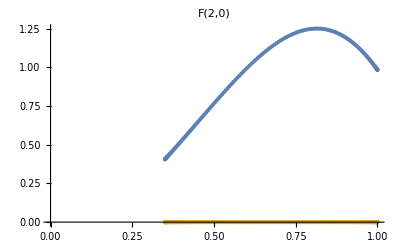

```mathematica
(* plot chosen component *)
data=NChebevalC[First[𝒱]/.out][xk];
interp=Interpolation[{rk,data}ᵀ];
Show[Plot[{Re[interp[r]],Im[interp[r]]},{r,rk[[1]],1},PlotRange->{{0,1},All}],ListPlot[{{rk,Re[data]}ᵀ,{rk,Im[data]}ᵀ}],PlotLabel->First[𝒱]]
(*data=NChebevalC[Last[𝒱]/.out][rk];
interp=Interpolation[{rk,data}ᵀ];
Show[Plot[{Re[interp[r]],Im[interp[r]]},{r,rk[[1]],1},PlotRange->{{0,1},All}],ListPlot[{{rk,Re[data]}ᵀ,{rk,Im[data]}ᵀ}],PlotLabel->Last[𝒱]]*)
```

## Plot fields

```mathematica
ClearAll[up,ut,upint,utint,urint,ucint,upintconj,ucintconj,urintconj,utintconj,uout]
gridr=N@Subdivide[Sequence@@Sprouts`layer[1],100];
Block[{mode=pos,ℓ,𝓂,head,subset=Sprouts`layout⟦1⟧,listcomp,comp,ω=-√eig⟦pos⟧},
listcomp=GetComponent[eigv⟦mode⟧,subset,1,Sprouts`layout⟦1⟧,Sprouts`nr,Coordinates->"Spherical"];
Table[
head=Head[subset⟦i⟧];ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
comp=listcomp⟦i⟧;
Which[
SameQ[head,F],
up[ℓ,𝓂]=((Function[x,(NChebeval[Re@N@#][Sprouts`ufr[1][x]]+ⅈ NChebeval[N@Im@#][Sprouts`ufr[1][x]])]/@gridr)&@comp);
upint[ℓ,𝓂]=Interpolation[{gridr,up[ℓ,𝓂]}ᵀ];
upintconj[ℓ,𝓂]=Interpolation[{gridr,up[ℓ,𝓂]*}ᵀ];
urint[ℓ,𝓂]=Evaluate[(ℓ(ℓ+1))/# upint[ℓ,𝓂][#]]&;
urintconj[ℓ,𝓂]=Evaluate[(ℓ(ℓ+1))/# upintconj[ℓ,𝓂][#]]&;
ucint[ℓ,𝓂]=Evaluate[(upint[ℓ,𝓂][#])/#+upint[ℓ,𝓂]'[#]]&;
ucintconj[ℓ,𝓂]=Evaluate[(upintconj[ℓ,𝓂][#])/#+upintconj[ℓ,𝓂]'[#]]&,
SameQ[head,G],
ut[ℓ,𝓂]=((Function[x,(NChebeval[Re@N@#][Sprouts`ufr[1][x]]+ⅈ NChebeval[N@Im@#][Sprouts`ufr[1][x]])]/@gridr)&@comp);
utint[ℓ,𝓂]=Interpolation[{gridr,ut[ℓ,𝓂]}ᵀ];
utintconj[ℓ,𝓂]=Interpolation[{gridr,ut[ℓ,𝓂]*}ᵀ];
];
uout[-1][ℓ,𝓂]=Evaluate[√((ℓ(ℓ+1))/2)(ucint[ℓ,𝓂][#]-ⅈ utint[ℓ,𝓂][#])]&;uout[0][ℓ,𝓂]=Evaluate[urint[ℓ,𝓂][#]]&;uout[+1][ℓ,𝓂]=Evaluate[√((ℓ(ℓ+1))/2)(ucint[ℓ,𝓂][#]+ⅈ utint[ℓ,𝓂][#])]&;

,{i,1,Length[subset]}]
];
```

```mathematica
urint[ℓ_,𝓂_][r_]:=0;
ucint[ℓ_,𝓂_][r_]:=0;
upint[ℓ_,𝓂_][r_]:=0;
utint[ℓ_,𝓂_][r_]:=0;
urintconj[ℓ_,𝓂_][r_]:=0;
ucintconj[ℓ_,𝓂_][r_]:=0;
upintconj[ℓ_,𝓂_][r_]:=0;
utintconj[ℓ_,𝓂_][r_]:=0;
```

```mathematica
ClearAll[Y]
Y[ℓ_,𝓂_,θ_,ϕ_]:=Y[ℓ,𝓂,θ,ϕ]=√((4π)/(2 ℓ+1))SphericalHarmonicY[ℓ,𝓂,θ,ϕ]
```

```mathematica
gridθ=Range[0.,π,π/100];
Block[{ℓ,𝓂,subset=Sprouts`layout⟦1⟧,ϕ=0},
gridur=Total@Quiet@Table[
ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
Re@Which[
SameQ[{ℓ,𝓂},{0,0}],uout[0][ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ],
SameQ[𝓂,0],uout[0][ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ],
True,2*uout[0][ℓ,𝓂][gridr]⊗Y[ℓ,𝓂,gridθ,ϕ]
]/.Indeterminate->(0.+ⅈ 0.)/.ComplexInfinity->(0.+ⅈ 0.)
,{i,1,Length[subset]}];
griduθ=Total@Quiet@Table[
ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
(√2)/2 Re@Which[
SameQ[{ℓ,𝓂},{0,0}],0.+ⅈ 0.,
SameQ[𝓂,0],uout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]-uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ],
True,2(uout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]-uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ])
]/.Indeterminate->(0.+ⅈ 0.)/.ComplexInfinity->(0.+ⅈ 0.)
,{i,1,Length[subset]}];
griduϕ=Total@Quiet@Table[
ℓ=subset⟦i⟧/.f_[l_,m_]->l;𝓂=subset⟦i⟧/.f_[l_,m_]->m;
(√2)/2 Im@Which[
SameQ[{ℓ,𝓂},{0,0}],0.+ⅈ 0.,
SameQ[𝓂,0],uout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]+uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ],
True,2(uout[-1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,-1,𝓂},gridθ,ϕ]+uout[+1][ℓ,𝓂][gridr]⊗WignerD[{ℓ,+1,𝓂},gridθ,ϕ])
]/.Indeterminate->(0.+ⅈ 0.)/.ComplexInfinity->(0.+ⅈ 0.)
,{i,1,Length[subset]}];
];
griduρ=(gridurᵀ*Sin[gridθ]+griduθᵀ*Cos[gridθ])ᵀ;
griduz=(gridurᵀ*Cos[gridθ]-griduθᵀ*Sin[gridθ])ᵀ;
```

```mathematica
coord[r_,θ_,ϕ_]:=
{r Cos[ϕ] Sin[θ],r Sin[θ] Sin[ϕ],r Cos[θ] };
ClearAll[StreamMeridPlot,MeridPlot]
StreamMeridPlot[rj_List,θk_List,ϕ_,{v1_,v2_,s_},opts___]:=
Module[{nr=Length[rj],nθ=Length[θk],tab,max=If[Max@Abs[s]≠0,Max@Abs[s],1]},
tab=Flatten[Table[{{√((coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦1⟧)^2+(coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦2⟧)^2),coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦3⟧},{{v1⟦j,k⟧,v2⟦j,k⟧},s⟦j,k⟧}},{j,1,nr},{k,1,nθ}],1];
tab;
ListStreamDensityPlot[tab,ColorFunction->(Lighter[ColorData["ThermometerColors"][Rescale[#,{-max,max} ]],0.1]&),ColorFunctionScaling->False,opts]]
coord[r_,θ_,ϕ_]:=
{Abs[r] Cos[ϕ] Sin[θ],Abs[r] Sin[θ] Sin[ϕ],Abs[r] Cos[θ] };
MeridPlot[rj_List,θk_List,mat_,ϕ_,opts___]:=
Module[{nr=Length[rj],nθ=Length[θk],tab,max=If[Max@Abs[mat]≠0,Max@Abs[mat],1]},
tab=Flatten[Table[{Sign[rj⟦j⟧] √((coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦1⟧)^2+(coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦2⟧)^2),coord[rj⟦j⟧,θk⟦k⟧,ϕ]⟦3⟧,mat⟦j,k⟧},{j,1,nr},{k,1,nθ}],1];
ListContourPlot[tab,ColorFunction->(ColorData["ThermometerColors"][Rescale[#,{-max,max} ]]&),ColorFunctionScaling->False,opts]]
```

```mathematica
<<MaTeX`
```

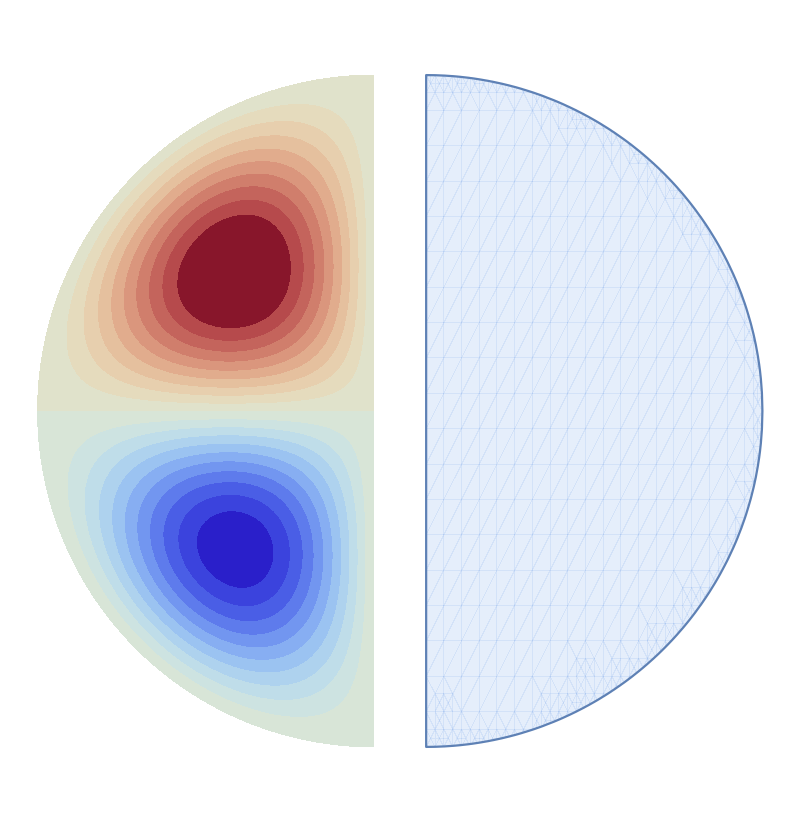

```mathematica
plot=Show[
GraphicsGrid[{{
Show[MeridPlot[-gridr,gridθ,griduϕ,0,AspectRatio->2,PlotRangePadding->None,Frame->False,Contours->20,PlotRange->All,ContourStyle->None,RegionFunction->Function[{x,y,z},First[Sprouts`domain]<Norm[{x,y}]<Last[Sprouts`domain]]],PlotLabel->MaTeX["B_\\phi",Magnification->1]],
Show[StreamMeridPlot[gridr,gridθ,0,{griduρ,griduz,griduϕ},AspectRatio->2,PlotRangePadding->None,Frame->False,PlotRange->All,StreamScale->Medium,StreamStyle->Black,RegionFunction->Function[{x,y,z},First[Sprouts`domain]<Norm[{x,y}]<Last[Sprouts`domain]]],PlotLabel->MaTeX["\\mathbf{B}",Magnification->1]]}},Spacings->-20],PlotLabel->MaTeX["\\lambda="<>ToString[λ/.(*parameters*)λ->-Chop@N[eig⟦pos⟧,5]],Magnification->1.5]]
```